```mathematica
bbva=FinancialData["BBVA.MC",{2000,01,01}]
```

{{{2000,1,3},6.85926},{{2000,1,4},6.68027},{{2000,1,5},6.53028},{{2000,1,7},6.61255},{{2000,1,10},6.50611},{{2000,1,11},6.3755},{{2000,1,12},6.34705},{{2000,1,13},6.1912},{{2000,1,14},6.31293},4429,{{2017,2,2},6.127},{{2017,2,3},6.182},{{2017,2,6},6.12},{{2017,2,7},6.108},{{2017,2,8},6.032},{{2017,2,9},6.053},{{2017,2,10},5.973},{{2017,2,13},6.06}}
 |  |  |  |

```mathematica
bbvaEMD=emd[bbva[[All,2]]]
```

{1}
 |  |  |  |

```mathematica
Dimensions[bbvaEMD]
```

{10,4446}

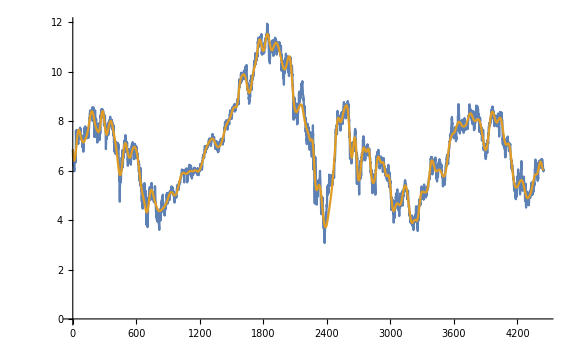

```mathematica
ListLinePlot[{bbva[[All,2]],Plus@@bbvaEMD[[-6;;-1]]}]
```

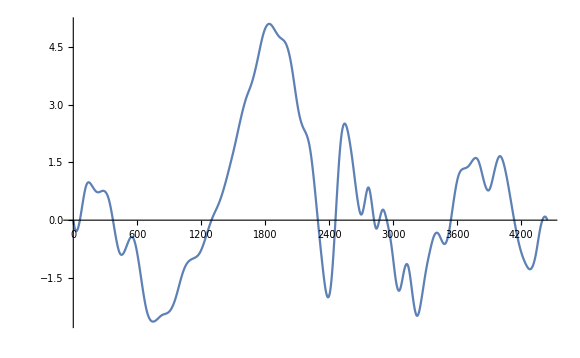

```mathematica
ListLinePlot[Plus@@bbvaEMD[[6;;8]]]
```

```mathematica
MatrixForm@Table[Plus@@(bbvaEMD[[i,j]] bbvaEMD[[j,i]]),{i,9},{j,9}]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.000695538 | -0.000440315 | -0.00619969 | -0.00421435 | -0.0000410572 | 0.000502923 | -0.000267413 | -0.0000350831
0. | -0.000440315 | 0.000153123 | -0.0035542 | -0.00670602 | -0.00404657 | -0.00124215 | 0.000564585 | 0.000169561
0. | -0.00619969 | -0.0035542 | 0.0393903 | 0.0320053 | 0.0138558 | 0.00376507 | -0.00199448 | -0.00116907
0. | -0.00421435 | -0.00670602 | 0.0320053 | 0.030215 | 0.0147781 | 0.00439677 | -0.00258288 | -0.00166433
0. | -0.0000410572 | -0.00404657 | 0.0138558 | 0.0147781 | 0.00789988 | 0.00247809 | -0.0015521 | -0.00105643
0. | 0.000502923 | -0.00124215 | 0.00376507 | 0.00439677 | 0.00247809 | 0.000786556 | -0.000502656 | -0.000344658
0. | -0.000267413 | 0.000564585 | -0.00199448 | -0.00258288 | -0.0015521 | -0.000502656 | 0.000330554 | 0.000230251
0. | -0.0000350831 | 0.000169561 | -0.00116907 | -0.00166433 | -0.00105643 | -0.000344658 | 0.000230251 | 0.000160785)

```mathematica
z=bbvaEMD+hilbert/@bbvaEMD I
```

{{0.-0.00627409 ⅈ,0.0301636+0.020051 ⅈ,-0.0458336+0.0133626 ⅈ,0.0515415-0.0292537 ⅈ,4438,-0.0287326-0.00540041 ⅈ,0.0329423+0.00135349 ⅈ,-0.0262306+0.0236986 ⅈ,0.-0.0140018 ⅈ},8,{1}}
 |  |  |  |

```mathematica
a=Abs/@z
```

{{0.00627409,0.03622,0.0477418,0.0592647,0.0942939,0.0802138,0.0568388,0.0542774,4430,0.0304516,0.0247408,0.0207024,0.0271666,0.0292357,0.03297,0.0353507,0.0140018},8,{1}}
 |  |  |  |

```mathematica
args=unwrap/@Arg[z]
```

{{-1.5708,0.586668,2.85791,5.76695,8.10938,10.3139,13.0288,15.752,18.4302,4428,7044.56,7047.16,7044.11,7047.11,7044.09,7046.78,7049.77,7052.14,7054.45},8,{1}}
 |  |  |  |

```mathematica
wargs=MovingMap[((-#[[1]]+8 #[[2]]+0 #[[3]]-8 #[[4]]+#[[5]])/12 )&,#,Quantity[5,"Events"]]&/@args
```

{{-0.38753,-0.329491,-0.329174,-0.380003,-0.172745,-0.184617,-0.16173,4287,0.481698,0.528909,-1.68356,0.463773,0.384376,-0.0637655,0.225568},8,{1}}
 |  |  |  |

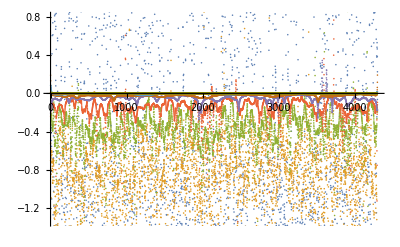

```mathematica
ListPlot[wargs]
```

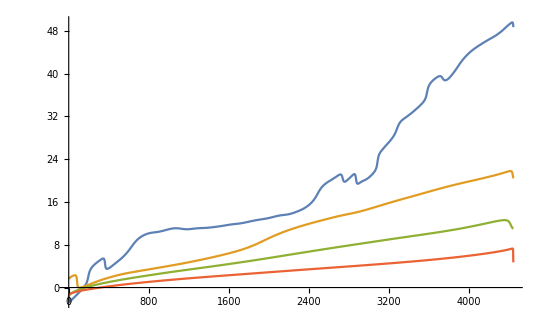

```mathematica
ListLinePlot[args[[6;;9]],PlotRange->All]
```

```mathematica
darg=differenceArgs/@Arg[z]
```

{{2.15746,2.27124,2.90904,2.34244,2.20454,2.71486,2.72326,2.67817,1.99571,4427,1.99859,2.60553,-3.04729,2.99615,-3.01957,2.68748,2.99687,2.3658,2.30553},9}
 |  |  |  |

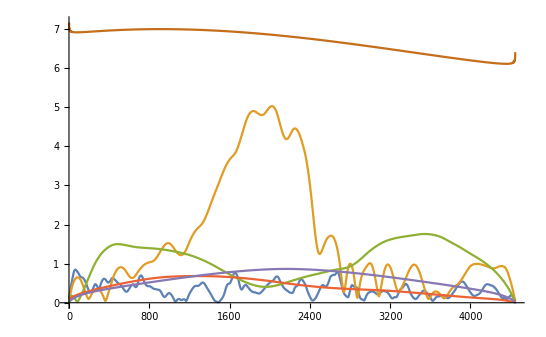

```mathematica
ListLinePlot[a[[5;;10]],PlotRange->All]
```

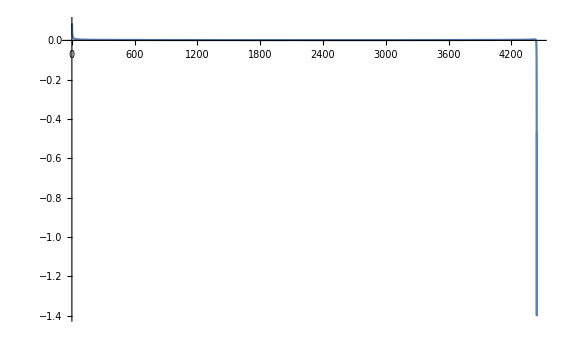

```mathematica
ListLinePlot[Differences/@args[[-2;;-2]],PlotRange->All]
```

```mathematica
lm=LinearModelFit[#,x,x]&/@args
```

{FittedModel[38.7998+1.57597 x],FittedModel[29.19+0.887835 x],FittedModel[24.7101+0.416384 x],FittedModel[13.7163+0.157733 x],FittedModel[-12.1044+0.0648312 x],FittedModel[-2.88414+0.0103037 x],FittedModel[-0.710253+0.00510662 x],FittedModel[-0.222392+0.00288659 x],FittedModel[-0.388743+0.00158959 x],FittedModel[-0.021582+9.70632×10^-6 x]}

```mathematica
Through[lm["RSquared"]]
```

{0.999786,0.999872,0.999077,0.998489,0.986472,0.904529,0.992282,0.997123,0.99054,0.0756021}

```mathematica
w=#[[2]]&/@Through[lm["BestFitParameters"]]
```

{1.57597,0.887835,0.416384,0.157733,0.0648312,0.0103037,0.00510662,0.00288659,0.00158959,9.70632×10^-6}

```mathematica
T=(2 N[Pi])/w
```

{3.98688,7.07698,15.0899,39.8343,96.9161,609.801,1230.4,2176.68,3952.71,647329.}

```mathematica
args[[1]][[1047;;1049]]
```

{1582.08,1583.48,1584.56}

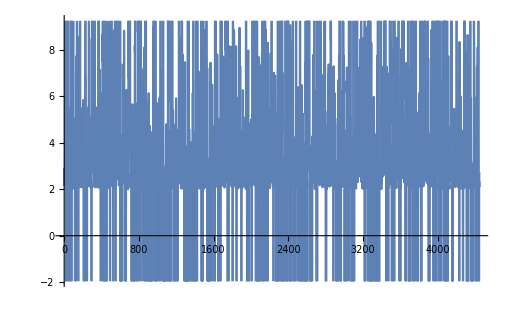

```mathematica
ListLinePlot[(2 N[Pi])/darg[[1;;1]]]
```

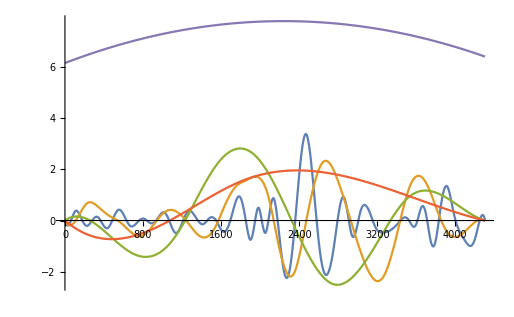

```mathematica
ListLinePlot[(*Plus@@*)bbvaEMD[[-5;;]]]
```

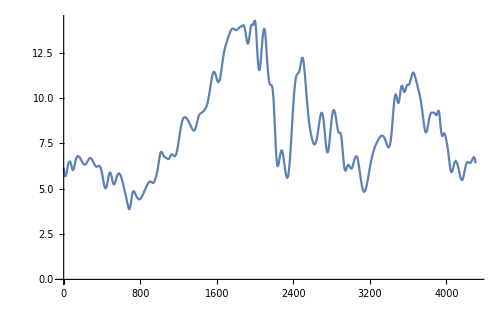

```mathematica
ListLinePlot[Plus@@bbvaEMD[[-6;;]]]
```

## Estic aquí

```mathematica
t=Table[Range[Length[a[[1]]]-1],9];
```

```mathematica
w=Differences/@args[[1;;9]];
```

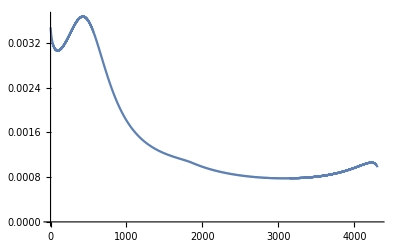

```mathematica
ListLinePlot[w[[9]],PlotRange->All]
```

```mathematica
e=a[[1;;9,2;;]]^2;
```

```mathematica
Dimensions[densityPlot]
```

{3,38736}

```mathematica
densityPlot=Transpose@(Flatten[#,1]&/@{t,w,e});
```

```mathematica
ListDensityPlot[densityPlot,ColorFunction->"DeepSeaColors"]
```

-Graphics-

```mathematica
ListContourPlot[densityPlot]
```

-Graphics-

```mathematica
Length[bbvaEMD]
```

10

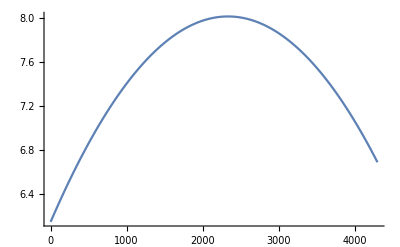

```mathematica
ListLinePlot[bbvaEMD[[10]]]
```

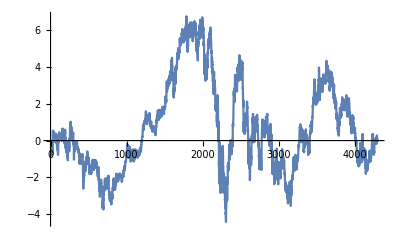

```mathematica
ListLinePlot[bbva[[All,2]]-bbvaEMD[[10]]]
```

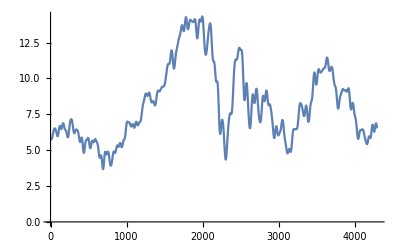

```mathematica
ListLinePlot[smoothDCT1[bbva[[All,2]],20]]
```

```mathematica
bbva20EMD=emd[smoothDCT1[bbva[[All,2]],20]]
```

{1}
 |  |  |  |

```mathematica
z20=bbva20EMD+hilbert/@bbva20EMD I
```

{{0.+0.0526063 ⅈ,-0.0195277+0.0689884 ⅈ,-0.0384789+0.0735461 ⅈ,-0.0568189+0.0750425 ⅈ,4294,-0.0238237+0.0220691 ⅈ,-0.0145009+0.0184171 ⅈ,0.+0.0273915 ⅈ},{1},3,{1}}
 |  |  |  |

```mathematica
a20=Abs/@z20
```

{{0.0526063,0.0716989,0.0830039,0.0941263,0.103984,0.113908,0.123479,4287,0.0614775,0.0550634,0.0483897,0.0408738,0.0324748,0.0234407,0.0273915},4,{1}}
 |  |  |  |

```mathematica
args20=unwrap/@Arg[z20]
```

{{1.5708,1.84664,2.05283,2.21886,2.3694,2.50248,2.62764,2.74268,4285,485.426,485.623,485.814,485.991,486.137,486.2,486.043,485.376},5}
 |  |  |  |

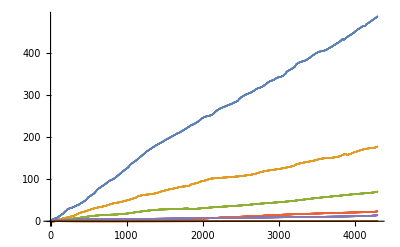

```mathematica
ListPlot[args20,PlotRange->All]
```

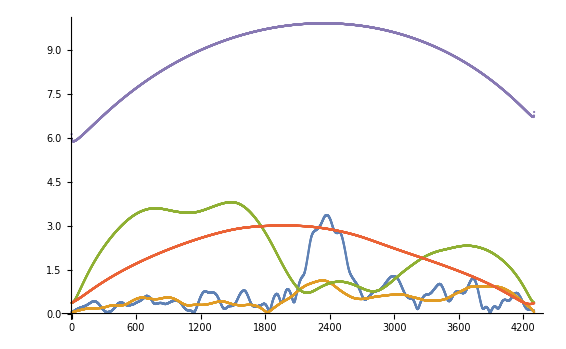

```mathematica
ListPlot[a20[[-5;;]],PlotRange->All]
```

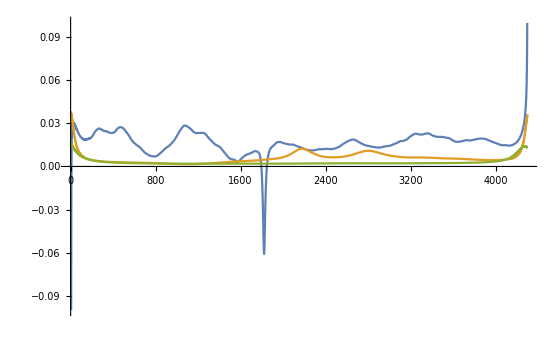

```mathematica
ListLinePlot[Differences/@args20[[3;;5]],PlotRange->{All,{-0.1,0.1}}]
```

```mathematica
lm20=LinearModelFit[#,x,x]&/@args20
```

{FittedModel[12.6566+0.110672 x],FittedModel[8.92013+0.039332 x],FittedModel[2.78059+0.01488 x],FittedModel[-2.48331+0.00565493 x],FittedModel[2.78987+0.00223357 x],FittedModel[-0.212601+0.0000988383 x]}

```mathematica
Dimensions[bbva20EMD]
```

{6,4301}

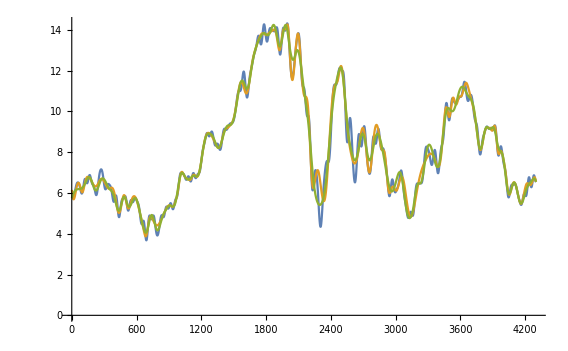

```mathematica
ListLinePlot[{(*bbva[[All,2]],*)smoothDCT1[bbva[[All,2]],20],Plus@@bbvaEMD[[-6;;]],Plus@@bbva20EMD[[-5;;]]}]
```

```mathematica
unwrap[arg_List,tol_Real:N[Pi]]:=Module[
{k=0.,alpha=tol,out=Table[0,Length[arg]]},
For[i=1,i≤Length[arg]-1,i++,
out[[i]]=arg[[i]]+2.*k*N[Pi];
If[Abs[arg[[i+1]]-arg[[i]]]>Abs[alpha],
If[arg[[i+1]]<arg[[i]],
k=k+1,
k=k-1
]
]
];
out[[-1]]=arg[[-1]]+2.*k*N[Pi];
out
];
```

```mathematica
lm=LinearModelFit[#,x,x]&/@args
```

{FittedModel[-37.2999+1.51009 x],FittedModel[60.5425+0.83278 x],FittedModel[34.5428+0.368585 x],FittedModel[10.0387+0.142481 x],FittedModel[3.64286+0.0522996 x],FittedModel[0.392659+0.0240992 x],FittedModel[-1.90915+0.00754165 x],FittedModel[1.22044+0.00279795 x],FittedModel[2.67007+0.00128001 x],FittedModel[-0.109497+0.000050905 x]}

```mathematica
1/20//N
```

0.05

```mathematica
argsFitted=Through[lm[#]]&/@Range[Length[args[[1]]]];
```

```mathematica
Dimensions[argsFitted]
```

{4301,10}

```mathematica
argsFitted=Transpose[argsFitted];
```

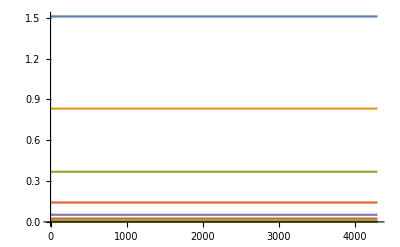

```mathematica
ListLinePlot[Differences/@argsFitted[[1;;10]],PlotRange->All]
```

```mathematica
emdFitted=Re[a Exp[I argsFitted]];
```

```mathematica
Dimensions[%]
```

{10,4301}

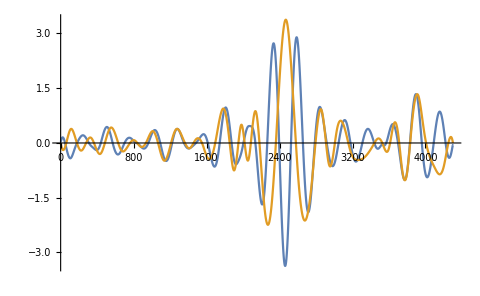

```mathematica
ListLinePlot[{Plus@@emdFitted[[-5;;-5]],Plus@@bbvaEMD[[-5;;-5]]},PlotRange->All]
```

```mathematica
san=FinancialData["SAN.MC",{2000,01,01}]
```

{{{2000,1,3},3.9963},{{2000,1,4},3.90149},{{2000,1,5},3.80667},{{2000,1,6},3.80667},{{2000,1,7},3.97523},{{2000,1,10},3.9401},{{2000,1,11},3.80667},{{2000,1,12},3.77155},4441,{{2017,2,2},5.289},{{2017,2,3},5.335},{{2017,2,6},5.222},{{2017,2,7},5.118},{{2017,2,8},5.047},{{2017,2,9},5.127},{{2017,2,10},5.041},{{2017,2,13},5.131}}
 |  |  |  |

```mathematica
sanEMD=emd[san[[All,2]]]
```

{1}
 |  |  |  |

```mathematica
Dimensions[sanEMD]
```

{10,4457}

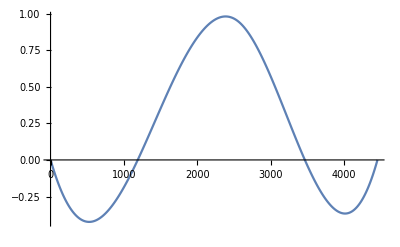

```mathematica
ListLinePlot[sanEMD[[9;;9]]]
```

```mathematica
Manipulate[ListLinePlot[sanEMD[[i;;j]]],{i,1,10,1},{j,1,10,1}]
```

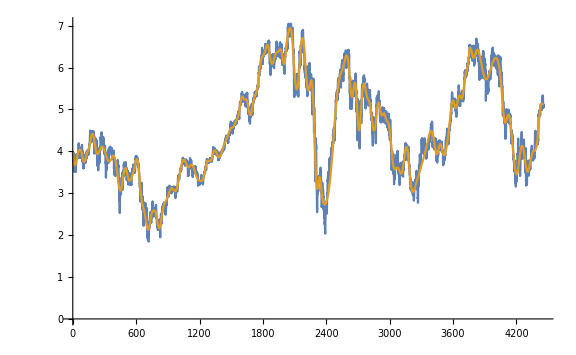

```mathematica
ListLinePlot[{san[[All,2]],Plus@@sanEMD[[5;;10]]}]
```

```mathematica
z=sanEMD+hilbert/@sanEMD I
```

{{0.+0.00671221 ⅈ,0.0143243+0.020332 ⅈ,-0.0452957+0.0462869 ⅈ,-0.0570992-0.0547688 ⅈ,4449,-0.0722469-0.0573181 ⅈ,0.0521703-0.0124798 ⅈ,-0.0280835+0.0272769 ⅈ,0.-0.014921 ⅈ},8,{1}}
 |  |  |  |

```mathematica
a=Abs/@z
```

{{0.00671221,0.0248712,0.0647625,0.0791198,0.0873214,0.122178,0.123017,0.112485,4441,0.118629,0.114838,0.0756835,0.0908438,0.0922225,0.0536422,0.0391499,0.014921},8,{1}}
 |  |  |  |

```mathematica
args=unwrap/@Arg[z]
```

{1}
 |  |  |  |

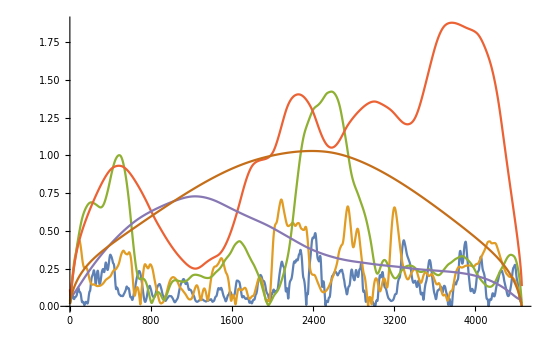

```mathematica
ListLinePlot[a[[4;;9]]]
```

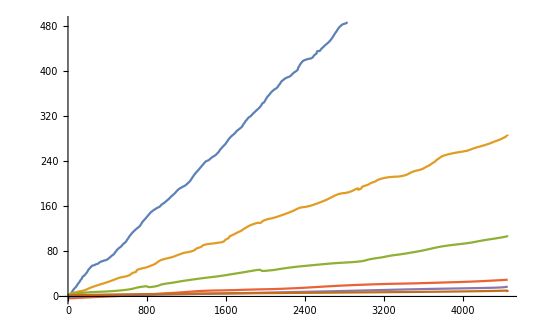

```mathematica
ListLinePlot[args[[4;;9]]]
```

```mathematica
lm=LinearModelFit[#,x,x]&/@args
```

{FittedModel[65.8839+1.56302 x],FittedModel[60.0137+0.864463 x],FittedModel[27.5731+0.397417 x],FittedModel[3.12662+0.170247 x],FittedModel[2.42311+0.0637989 x],FittedModel[0.114196+0.022817 x],FittedModel[-1.79638+0.0071932 x],FittedModel[-0.215979+0.00363734 x],FittedModel[2.76092+0.00155426 x],FittedModel[0.0610236-0.0000273771 x]}

```mathematica
Through[lm["RSquared"]]
```

{0.99939,0.99948,0.999051,0.999348,0.998671,0.99365,0.98934,0.99693,0.987984,0.15567}

```mathematica
w=#[[2]]&/@Through[lm["BestFitParameters"]]
```

{1.56302,0.864463,0.397417,0.170247,0.0637989,0.022817,0.0071932,0.00363734,0.00155426,-0.0000273771}

```mathematica
T=(2 N[Pi])/w
```

{4.01989,7.26831,15.8101,36.9064,98.4842,275.373,873.49,1727.41,4042.55,-229505.}

```mathematica
s1=Plus@@sanEMD[[5;;10]];
```

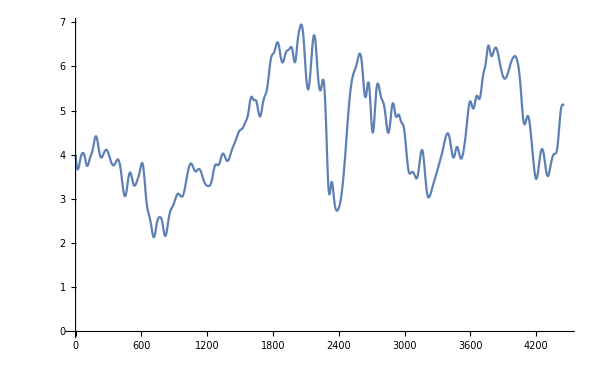

```mathematica
ListLinePlot[s1]
```

```mathematica
1/37//N
```

0.027027

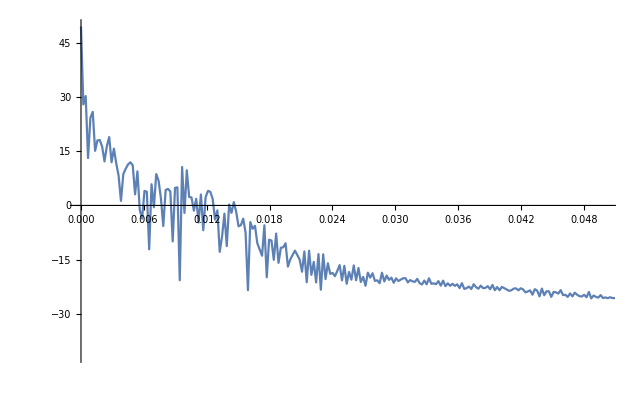

```mathematica
Periodogram[s1,PlotRange->{{0,0.05},All}]
```